Von Neumann Entropy

Definitionpaclet:Q3/tutorial/VonNeumannEntropy#67330687 | Quantum Mutual Informationpaclet:Q3/tutorial/VonNeumannEntropy#2123841012
Quantum Relative Entropypaclet:Q3/tutorial/VonNeumannEntropy#1419154497 |

The Shannon entropy is a measure of uncertainty associated with a classical probability distribution. We now generalize the notion to quantum states described by density operators.

ShannonEntropypaclet:Q3/ref/ShannonEntropyQ3 Package Symbol | The Shannon entropy of a probability distribution
VonNeumannEntropypaclet:Q3/ref/VonNeumannEntropyQ3 Package Symbol | The von Neumann entropy of a quantum state
MutualInformationpaclet:Q3/ref/MutualInformationQ3 Package Symbol | Classical and quantum mutual information

Q3 functions related to the von Neumann entropy.

Make sure that the Q3 package is loaded to use the demonstrations in this documentation.

```mathematica
<<Q3`
```

Throughout this document, symbol S will be used to denote qubits and Pauli operators on them. Similarly, symbol c will be used to denote complex-valued coefficients.

```mathematica
Let[Qubit,S]
Let[Complex,c]
```

Definition

A classical probability distribution is associated with a random variable choosing values from a set of outcomes. In quantum mechanics, a density operator is associated with an ensemble of quantum states. One can imagine a quantum information source that generates messages of “letters” each of which is chosen from the ensemble.

The von Neumann entropy of a quantum state ρ is defined by

S(ρ):=−Tr [ρ logρ] ,

where the logarithm is with respect to base 2. A basic approach to evaluate the above expression is to take the spectral decomposition

ρ=Σ_λ λλλ

where λ is the eigenvector of ρ with eigenvalue λ. Given that ρ is a positive operator, all the eigenvalues are non-negative, λ≥0. Then, the von Neumann entropy is given by

S(ρ)=-Σ_λ λlogλ .

In comparison with the Shannon entropy, the eigenvalues play the role of probabilities. For zero eigenvalues (λ=0), we put 0 log0=0.

For example, consider the density operator

ρ=1/2 I+1/4 Y≐1/4(2 | -ⅈ
ⅈ | 2) .

It has two eigenvalues 1/4 and 3/4, and the von Neumann entropy is given by

S(ρ)=1/2-3/4 log 3/4 .

The von Neumann entropy of any pure state |ψ⟩ vanishes,

S(ψψ)=0

because the only non-vanishing eigenvalue of ψψ is 1. Physically, this is because there is no ambiguity in the quantum state at hand. On the other hand, the von Neumann entropy of the maximally mixed state I/d, where d is the dimension of the Hilbert space, is given by

S(I/d)=logd .

Recalling that the Shannon entropy is the biggest for the uniform distribution, one can expect that logd is the maximum value that the von Neumann entropy can take. Indeed, we will later see that

0≤S(ρ)≤logd

for any quantum state.

Let us consider a simple example. The density operator describes an ensemble of two pure states 0 and +:=(0+1)/√2.

```mathematica
Clear[p]
vec=(Ket[]+Ket[S->1])/Sqrt[2];
rho=p*Dyad[Ket[],Ket[],S]+(1-p)*Dyad[vec,vec,S]
Matrix[rho]//MatrixForm
```

p 0_S0_S+(1-p) ((0_S0_S)/2+(0_S1_S)/2+(1_S0_S)/2+(1_S1_S)/2)

(1/2+p/2 | 1/2-p/2
1/2-p/2 | 1/2-p/2)

Here are the eigenvalues of the density operator.

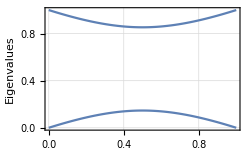

```mathematica
Plot[ProperValues[rho],{p,0,1},FrameLabel->{"p","Eigenvalues"}]
```

Here is the von Neumann entropy of the density operator as a function of p.

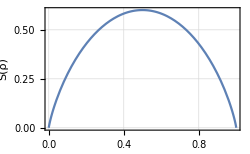

```mathematica
Plot[VonNeumannEntropy[rho],{p,0,1},FrameLabel->{"p","S(ρ)"}]
```

A convex linear superposition of different quantum states gives rise to another quantum state,

ρ=Σ_j p_j ρ_j

where p_j are probabilities, that is, 0≤p_j≤1 and ∑_j p_j=1. Intuitively, we expect that the uncertainty about ρ is larger than the average uncertainty of individual ρ_j because we are not only ignorant of each state ρ_j but also of which of those states to be selected upon a random choice. This implies that the von Neumann entropy is a concave function of density operator,

Σ_j p_j S(ρ_j)≤S(∑_j p_j ρ_j) .

Following the above intuitive argument, we may add the Shannon entropy H({p_j}) to account for our ignorance of which to be selected from the ensemble of states ρ. One can show that if the states ρ are all distinguishable with certainty, then the addition of the contributions indeed gives the entropy of ρ. In general, however, it overestimates the von Neumann entropy of ρ, and we have the inequality

S(∑_j p_j ρ_j)≤Σ_j p_j S(ρ_j)+H({p_j}) .

To prove the above two inequalities rigorously, we would need more mathematical tools and entropic relations to be discussed below. Interested readers are encouraged to try Problem 7.6 of the Quantum Workbookhttps://doi.org/10.1007/978-3-030-91214-7 after we introduce required materials.

Quantum Relative Entropy

### Definition

We introduce the relative von Neumann entropy as the quantum counterpart of the relative Shannon entropy. One can regard it as a measure of the closeness of two quantum states just as the relative Shannon entropy is a measure of closeness of two classical probability distribution. However, like the relative Shannon entropy, relative von Neumann entropy is of little use in its own right. Rather, it provides powerful mathematical techniques that can be employed to investigate various entropic quantities and relations.

Let ρ and σ be two density operators on a vector space. We define the relative von Neumann entropy or simply relative entropy of ρ to σ by

S(ρ∥σ):=Tr[ρlogρ]-Tr[ρlogσ]=-S(ρ)-Tr[ρlogσ] .

We have already explained how to calculate the first term. The second term is more complicated to calculate. One way is to use the spectral decomposition of σ

σ=Σ_s sss ,

where s is an eigenstate with eigenvalue s of σ,

S(ρ∥σ)=-S(ρ)-Σ_s sρslogs .

We note that when an eigenvalue s of σ vanishes with the finite expectation value sρs, the second term diverges to ∞. In general, the relative entropy diverges when the support of ρ (i.e., the subspace belonging to non-zero eigenvalues) has a finite overlap with the null space of σ (i.e., the subspace belonging to eigenvalue zero).

For example, consider the two quantum states

ρ=1/2 I+1/4 Z≐(3/4 | 0
0 | 1/4) ,    σ=1/2 I+1/4 X≐(1/2 | 1/4
1/4 | 1/2) .

Both have the same eigenvalues 3/4 and 1/4 and hence the same von Neumann entropy

S(ρ)=S(σ)=1/2-3/4 log 3/4 .

On the other hand, the eigenvectors of σ are ±:=(0±1)/√2. Therefore, the relative entropy is given by

S(ρ∥σ)=-S(ρ)-+ρ+log 3/4--ρ-log 1/4=1/2-1/4 log 3/4 .

Now, consider still another density operator

τ=1/2 I+1/2 Y≐1/2(1 | -ⅈ
ⅈ | 1) .

It has two eigenvectors, L:=(0+ⅈ1)/√2 with eigenvalue 1 and L:=(0-ⅈ1)/√2 with eigenvalue 0. That is, τ has a null space spanned by R. Note that both ρ and σ have a finite overlap, RρR=RσR=1/2. The relative entropies of both ρ and σ to τ diverge, S(ρ∥τ)=S(σ∥τ)=∞, whereas S(τ∥ρ)
and S(τ∥σ) are finite.

### Examples

Consider a quantum state described by the following density operator.

```mathematica
rho=1/2+S[3]/4;
rho//Matrix//MatrixForm
```

(3/4 | 0
0 | 1/4)

Here is the von Neumann entropy of the above state.

```mathematica
VonNeumannEntropy[rho]
```

1/2+(3 Log[4/3])/(4 Log[2])

Consider another density operator.

```mathematica
sgm=S[6]**rho**S[6];
sgm//Matrix//MatrixForm
```

(1/2 | 1/4
1/4 | 1/2)

It has the same eigenvalues as rho and hence the same von Neumann entropy.

```mathematica
VonNeumannEntropy[sgm]
```

1/2+(3 Log[4/3])/(4 Log[2])

This gives the relative entropy of rho to sgm.

```mathematica
VonNeumannEntropy[rho,sgm]
```

1/2-Log[4/3]/(4 Log[2])

Let us consider still another density operator.

```mathematica
tau=1/2+S[2]/2;
tau//Matrix//MatrixForm
```

(1/2 | -ⅈ/2
ⅈ/2 | 1/2)

Note that it has one zero eigenvalue.

```mathematica
{val,vec}=ProperSystem[tau];
val
```

{1,0}

The null space (the subspace belonging to the zero eigenvalue) is spanned by (i0+1)/√2.

```mathematica
vec=KetNormalize/@vec
```

{-(ⅈ 0_S)/(√2)+(1_S)/(√2),(ⅈ 0_S)/(√2)+(1_S)/(√2)}

Note that the both density operators rho and sgm has a finite overlap with the null space of tau.

```mathematica
Dagger[vec[[2]]]**sgm**vec[[2]]
Dagger[vec[[2]]]**sgm**vec[[2]]
```

1/2

1/2

This means that the relative entropy of rho and smg to tau diverge (however close rho and smg may look to tau).

```mathematica
VonNeumannEntropy[rho,tau]
VonNeumannEntropy[sgm,tau]
```

∞

∞

On the other hand, the relative entropies of tau to rho and sgm are finite.

```mathematica
VonNeumannEntropy[tau,rho]
VonNeumannEntropy[tau,sgm]
```

1+Log[4/3]/(2 Log[2])

1+Log[4/3]/(2 Log[2])

### Properties

When ρ and σ are diagonal simultaneously,

ρ=Σ_j λ_j r_j λ_j ,     σ=Σ_j λ_j s_j λ_j

the relative von Neumann entropy is simple to evaluate and reduces to the relative Shannon entropy,

S(ρ∥σ)=H({r_j}∥{s_j}) .

The power of the relative entropy as a mathematical tool comes from Klein’s inequality,

S(ρ∥σ) ≥ 0

with equality if and only if ρ=σ, to be compared to Gibbs' inequality for the relative Shannon entropy. Like Gibbs’ inequality, one can prove Klein’s inequality based on the convexity of the logarithm function. But it is slightly more complicated since ρ and σ do not commute with each other in general. Interested readers are referred to Problem 7.3 of the Quantum Workbookhttps://doi.org/10.1007/978-3-030-91214-7.

For a basic application of Klein’s inequality, we put σ =I/d, where d is the dimension of the Hilbert space (that is,  σ is the maximally mixed state), into the inequality. It follows that

S(ρ∥σ)=-S(ρ)-Trρ log 1/d=-S(ρ)+logd≥0

with equality if and only if ρ=I/d. This proves the deferred claim that

0≤S(ρ)≤logd .

Quantum Mutual Information

### Definition

For the Shannon entropy, we introduced the joint and conditional entropies by considering multiple random variables. To generalize those concepts to the quantum entropy, we consider a composite system of two subsystems A and B.

Suppose that ρ_AB is a density operator of the total system. The quantum joint entropy, or simply joint entropy if there is no risk of confusion, of A and B is nothing but the von Neumann entropy associated with ρ_AB,

S(A,B):=S(ρ_AB)=-Tr[ρ_AB log ρ_AB] .

For a product state ρ_AB=ρ_A⊗ρ_B, the joint entropy is the sum of the entropies of the individual entropies

S(ρ_A⊗ρ_B)=S(ρ_A)+S(ρ_B) .

In analogy with the classical case, we also define the quantum conditional entropy of A on B by

S(A|B):=S(A,B)-S(B) ,

and the quantum mutual information of A and B by

S(A:B):=S(A)+S(B)-S(A,B)=S(A)-S(A|B)=S(B)-S(B|A) .

Here, S(A):=S(ρ_A) and S(B):=S(ρ_B) are associated with the reduced density operators

ρ_A=Tr_B ρ_AB ,    ρ_B=Tr_A ρ_AB ,

respectively. In comparison with the classical case, ρ_AB corresponds to a joint probability distribution p(x,y), and ρ_A and ρ_B to p(x) and p(y), respectively. Note that for a pure state, we have

S(A)=S(B)

and hence

S(A:B)=2S(A)=2S(B) .

### Examples

Consider a density matrix in a 3⊗2 bi-partite system.

```mathematica
mat=RandomPositive[6];
mat=Chop[mat/Tr[mat]];
```

Take a look at the part of the matrix.

```mathematica
mat[[;;UpTo[4],;;UpTo[4]]]//MatrixForm
```

(0.207974 | -0.0315317-0.0132924 ⅈ | -0.0130907-0.112342 ⅈ | 0.0255377-0.0645811 ⅈ
-0.0315317+0.0132924 ⅈ | 0.230224 | 0.0622063-0.0849198 ⅈ | 0.000600014+0.0412476 ⅈ
-0.0130907+0.112342 ⅈ | 0.0622063+0.0849198 ⅈ | 0.17455 | 0.0407559+0.001773 ⅈ
0.0255377+0.0645811 ⅈ | 0.000600014-0.0412476 ⅈ | 0.0407559-0.001773 ⅈ | 0.15134)

Calculate the mutual information between the two parts.

```mathematica
MutualInformation[mat,{3,2},{2}]//Chop
```

0.37928

Suppose that the total system in the above example consists of a qutrit (referred to by A) and qubit (referred to by S)

```mathematica
Let[Qubit,S]
Let[Qudit,A]
```

Construct the density operator corresponding to the matrix in the above.

```mathematica
rho=ExpressionFor[mat,{A,S}]//Elaborate
```

0.174314-(0.0297541-0.0514617 ⅈ) 10-(0.0204307+0.0066012 ⅈ) 20-(0.0297541+0.0514617 ⅈ) 01+0.000634505 11+(0.00619153+0.0290281 ⅈ) 21-(0.0204307-0.0066012 ⅈ) 02+(0.00619153-0.0290281 ⅈ) 12-0.0235772 22+(0.00479349-0.0194324 ⅈ) S^X10+(0.0151998-0.0248145 ⅈ) S^X20+(0.00479349+0.0194324 ⅈ) S^X01+(0.104696-3.03577×10^-18 ⅈ) S^X11-(0.0267902+0.00668767 ⅈ) S^X21+(0.0151998+0.0248145 ⅈ) S^X02-(0.0267902-0.00668767 ⅈ) S^X12+(0.0517502-6.93889×10^-18 ⅈ) S^X22-(0.0392347+0.0470432 ⅈ) S^Y10-(0.0138725+0.0288332 ⅈ) S^Y20-(0.0392347-0.0470432 ⅈ) S^Y01+(0.0742463+0. ⅈ) S^Y11-(0.0283586+0.0149719 ⅈ) S^Y21-(0.0138725-0.0288332 ⅈ) S^Y02-(0.0283586-0.0149719 ⅈ) S^Y12+(0.150193+0. ⅈ) S^Y22-(0.00774265+0.0123252 ⅈ) S^Z10-(0.0205295+0.0302787 ⅈ) S^Z20-(0.00774265-0.0123252 ⅈ) S^Z01-0.00174906 S^Z11-(0.0439455-0.0363777 ⅈ) S^Z21-(0.0205295-0.0302787 ⅈ) S^Z02-(0.0439455+0.0363777 ⅈ) S^Z12+0.0190121 S^Z22-(0.0384653-6.93889×10^-18 ⅈ) S^X-(0.0782502+0. ⅈ) S^Y+0.00734562 S^Z

Calculate the mutual information between the qutrit and qubit.

```mathematica
MutualInformation[rho,{S}]
```

0.37928

Let us take an example of  closer correlation.

```mathematica
Let[Qubit,S]
```

Consider a maximally entangled state.

```mathematica
ket=First@BellState[S@{1,2}]
```

(0_(,,S_(,,1))0_(,,S_(,,2))+1_(,,S_(,,1))1_(,,S_(,,2)))/(√2)

Construct the density operator.

```mathematica
rho=ket**Dagger[ket]
```

1/2 0_(,,S_(,,1))0_(,,S_(,,2))0_(,,S_(,,1))0_(,,S_(,,2))+1/2 0_(,,S_(,,1))0_(,,S_(,,2))1_(,,S_(,,1))1_(,,S_(,,2))+1/2 1_(,,S_(,,1))1_(,,S_(,,2))0_(,,S_(,,1))0_(,,S_(,,2))+1/2 1_(,,S_(,,1))1_(,,S_(,,2))1_(,,S_(,,1))1_(,,S_(,,2))

Calculate the mutual information between the two qubits.

```mathematica
MutualInformation[rho,S[1]]
```

2

### Properties

It is worth noticing that the physical interpretations of classical joint and conditional entropies defy our expectation when applied to the quantum joint and conditional entropies. For example, unlike the solid inequality H(X)≤H(X,Y) for classical random variables X and Y , the analogous inequality S(A)≤S(A,B) does not hold. Equivalently, the conditional entropy is not necessarily positive, S(A|B) ≱ 0; hence, the the data compression inequality H(X:Y)⩽ H(X) is not generalized to quantum information, S(A:B)≰S(A) nor S(A:B)≰S(B). Such violations are usually attributed to quantum entanglement, a special kind of correlation between subsystems (see the tutorial “Entanglement and Entropy” for more details). For example, consider the quantum state (00+11)/√2. It is a pure state and certainly S(A,B)=0. However, ρ_A=ρ_B=I/2 and hence S(A)=S(B)=1> S(A,B).

Nevertheless, the quantum mutual information is always non-negative. It leads to the subadditivity

S(ρ_AB)≤S(ρ_A)+S(ρ_B) .

This can be easily seen by employing Klein’s inequality (see Problem 7.5 of the Quantum Workbookhttps://doi.org/10.1007/978-3-030-91214-7).

The subadditivity further implies an interesting property of the von Neumann entropy. Introduce a third system C, and consider a purification Ψ_ABC of ρ_AB into 𝒱_A⊗𝒱_B⊗𝒱_C. We employ the subadditivity inequality to get

S(A,C)≤S(A)+S(C) .

Since Ψ_ABC is a pure state,

S(A,B)=S(C) ,     S(A,C)=S(B).

Therefore, it follows that

S(B)-S(A)≤S(A,B) .

Similarly, from S(B,C)≤S(B)+S(C), we have

S(A)-S(B)≤S(A,B) .

Combining the above two inequalities, we have the so-called triangle inequality for the von Neumann entropy

|S(ρ_A)-S(ρ_B)|≤S(ρ_AB) .

There are many more interesting and useful properties of the quantum joint and conditional entropies and mutual information. Here, we have discussed a minimal set of them. Interested readers are referred to Wehrl (1978)https://doi.org/10.1103/RevModPhys.50.221.

| Related Guides
▪Quantum Information Systems

| Related Tech Notes
▪Quantum Information Theory
▪Quantum Information Systems with Q3

| Related Links
▪A. Wehrl, Reviews of Modern Physics 50, 221 (1978)https://doi.org/10.1103/RevModPhys.50.221, “General properties of entropy.”
▪M. Nielsen and I. L. Chuang (2022)https://doi.org/10.1017/CBO9780511976667, Quantum Computation and Quantum Information (Cambridge University Press).
▪Mahn-Soo Choi (2022)https://doi.org/10.1007/978-3-030-91214-7, A Quantum Computation Workbook (Springer).